```mathematica
Biseccio[f_,{a_,b_,M_}]:=Module[{an,bn,xn},
an=a;
bn=b;
For[i=1,i≤M,i++,
xn=(an+bn)/2;
If[f[xn]==0,Break[],
If[f[an]*f[xn]<0, bn=xn,
If[f[xn]*f[bn]<0,an=xn]
]
]
];
N[xn,20]
]
```

```mathematica
f[x_]= x^3 - 5
```

-5+x^3

```mathematica
Reduce[2/2^n<10^(-11),n,Reals]
```

n>(12 Log[2]+11 Log[5])/Log[2]

```mathematica
N[%]
```

n>37.5412

```mathematica
Biseccio[f,{0,2,38}]
```

1.7099759466727846302

```mathematica
N[5^(1/3),20]
```

1.7099759466766969894

Syntax::sntxf: "N[" cannot be followed by "[%], 20]"\"\<\>\".

```mathematica
Newton[f_,x0_,M_]:=Module[{xn},
xn=x0;
For[i=1, i≤M, i++,
xn=xn-f[xn]/f'[xn]
];
N[xn,20]
]
```

```mathematica
h[x_]= 3x-x^3+4
```

4+3 x-x^3

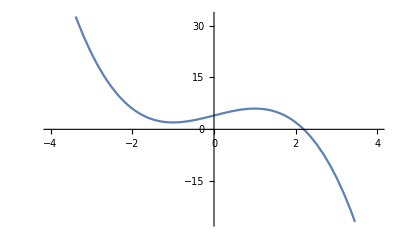

```mathematica
Plot[h[x],{x,-4,4}]
```

```mathematica
Newton[h,2,4]
```

2.1958233454456516143

```mathematica
NSolve[h[x]==0,x,WorkingPrecision->20]
```

{{x→-1.0979116727228235764-0.7850032632435902184 ⅈ},{x→-1.0979116727228235764+0.7850032632435902184 ⅈ},{x→2.1958233454456471528}}

```mathematica
g[x_]= x^2-Cos[x]+Sin[x]
```

x^2-Cos[x]+Sin[x]

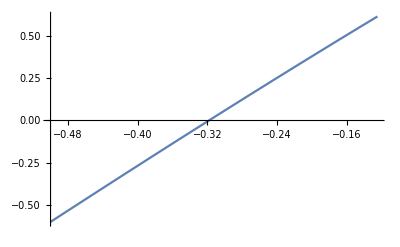

```mathematica
x^2-Cos[x]+Sin[x]

Plot[g'[x],{x,-0.5,-0.125}]
```

```mathematica
Reduce[(0.5-0.125)/2^n==10^(-11),n,Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n==35.1262

```mathematica
Biseccio[g',{-0.5,-0.125,36}]
```

```mathematica
-0.3183663254039857
```

```mathematica
Newton[g',-0.5,2]
```

-0.318367

```mathematica
NumberForm[-0.3183668642164842,20]
```

-0.3183668642164842

```mathematica
NumberForm[-0.31836632540266935,20]
```

-0.3183663254026694